```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/IR_RAMAN/ZrC/"];
zrcIR=Table[ReadList[{"initial_kp444_encut700-ENCUT_500_ediff6-PERF","initial_kp444_encut700-ENCUT_500_ediff6-FREN","initial_kp444_encut700-ENCUT_700_ediff7-PERF","initial_kp444_encut700-ENCUT_700_ediff7-FREN","initial_kp444_encut700-ENCUT_700_ediff7-C_VAC","initial_kp444_encut700-ENCUT_700_ediff7-Z_VAC"}[[i]],{Number,Number,Number}],{i,1,6}]
```

```mathematica
dataPerf500=Transpose@{Transpose[zrcIR[[1]]][[2]],Transpose[zrcIR[[1]]][[3]]};
dataFren500=Transpose@{Transpose[zrcIR[[2]]][[2]],Transpose[zrcIR[[2]]][[3]]};
dataPerf700=Transpose@{Transpose[zrcIR[[3]]][[2]],Transpose[zrcIR[[3]]][[3]]};
dataFren700=Transpose@{Transpose[zrcIR[[4]]][[2]],Transpose[zrcIR[[4]]][[3]]};
dataCvac700=Transpose@{Transpose[zrcIR[[5]]][[2]],Transpose[zrcIR[[5]]][[3]]};
dataZvac700=Transpose@{Transpose[zrcIR[[6]]][[2]],Transpose[zrcIR[[6]]][[3]]};
```

```mathematica
"Perfect ZrC - 500 and 700eV ENCUT:"
GraphicsGrid[{{ListPlot[dataPerf500,Filling->Axis],Show[ListPlot[dataPerf500,Filling->Axis],ListPlot[dataPerf700]]}},ImageSize->800];
"Defect Frenkel ZrC - 500 and 700eV ENCUT:"
GraphicsGrid[{{ListPlot[dataFren500,Filling->Axis],Show[ListPlot[dataFren500,Filling->Axis],ListPlot[dataFren700]]}},ImageSize->800];
"C_vac and Z_vac ZrC - 700eV ENCUT:"
GraphicsGrid[{{ListPlot[dataCvac700,Filling->Axis,PlotRange->All],ListPlot[dataZvac700,Filling->Axis,PlotRange->All]}}];
```

Perfect ZrC - 500 and 700eV ENCUT:

Defect Frenkel ZrC - 500 and 700eV ENCUT:

C_vac and Z_vac ZrC - 700eV ENCUT:

{Filling→Axis,PlotRange→{{500,950},All}}

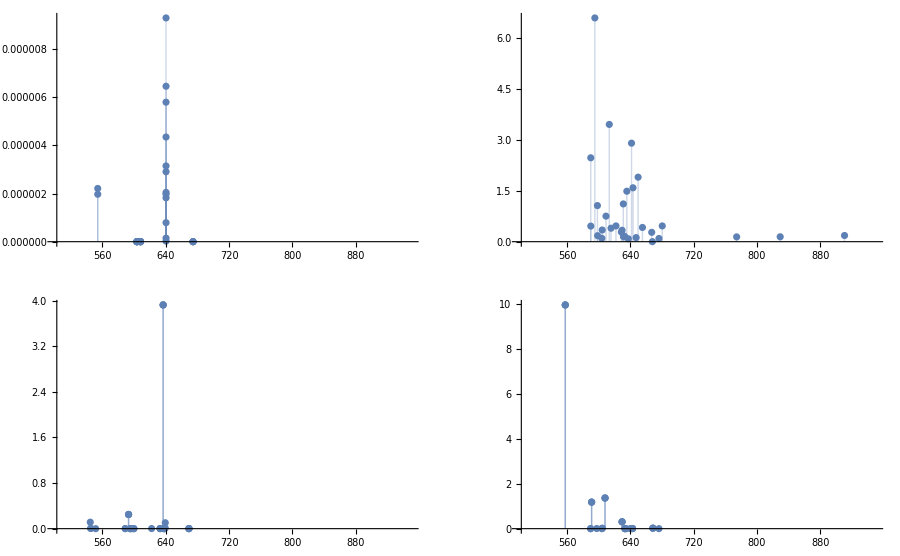

```mathematica
plotions={Filling->Axis,PlotRange->{{500,950},All}}
GraphicsGrid[{{ListPlot[dataPerf700,Evaluate@plotions],ListPlot[dataFren700,Evaluate@plotions]},{ListPlot[dataCvac700,Evaluate@plotions],ListPlot[dataZvac700,Evaluate@plotions]}},ImageSize->900]
```

```mathematica
plotops={PlotRange->{{500,950},All},AxesLabel->{"Energy\n (cm^-1)","Absorption\nintensity"}}
plotFun[{m_,h_},name_]:=Plot[h*PDF[NormalDistribution[m,2],x],{x,500,950},Evaluate@plotops,PlotLabel->name]
p1=Show[Table[plotFun[dataPerf700[[i]],"Perfect ZrC"],{i,1,Length[dataPerf700]}]];
p2=Show[Table[plotFun[dataFren700[[i]],"Frenkel ZrC"],{i,1,Length[dataFren700]}]];
p3=Show[Table[plotFun[dataCvac700[[i]],"C vacancy ZrC"],{i,1,Length[dataCvac700]}]];
p4=Show[Table[plotFun[dataZvac700[[i]],"Zr vacancy ZrC"],{i,1,Length[dataZvac700]}]];
```

{PlotRange→{{500,950},All},AxesLabel→{Energy
 (cm^-1),Absorption
intensity}}

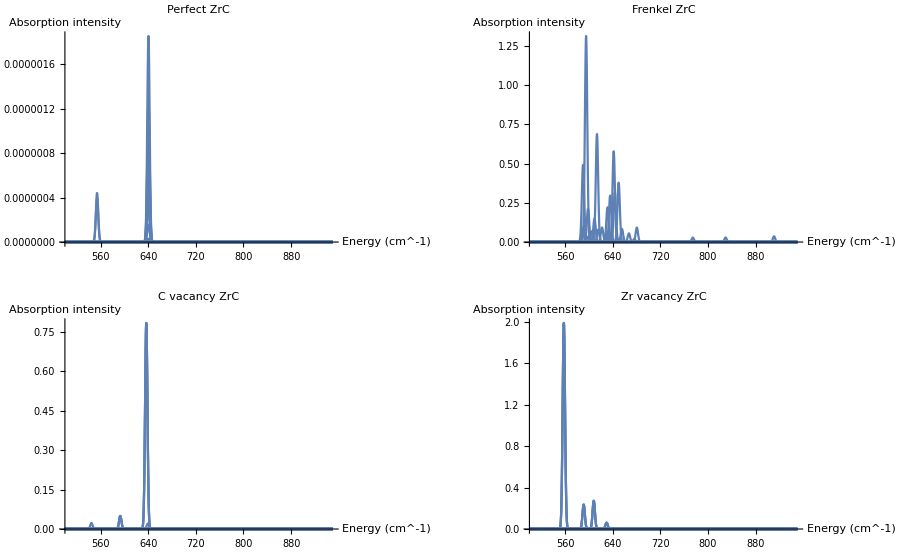

```mathematica
GraphicsGrid[{{p1,p2},{p3,p4}},ImageSize->900]
```

```mathematica
gauss[{m_,h_}]:=h*PDF[NormalDistribution[m,2],x]
plotops2={Ticks->{Automatic,None},PlotRange->All,AxesLabel->{"Energy\n(1/cm)","Relative cummulative \nabsorption intensity"},PlotRange->{{540,850},{Automatic}}};
plotFun2[file_,name_]:=Plot[10-Total[Table[gauss[file[[i]]],{i,1,Length[file]}]],{x,540,850},PlotLabel->name,Evaluate@plotops2];
```

```mathematica
p1=plotFun2[dataPerf700,"Perfect ZrC"];
p2=plotFun2[dataFren700,"Frenkel defect ZrC"];
p3=plotFun2[dataCvac700,"C vacancy ZrC"];
p4=plotFun2[dataZvac700,"Zr vacancy ZrC"];
```

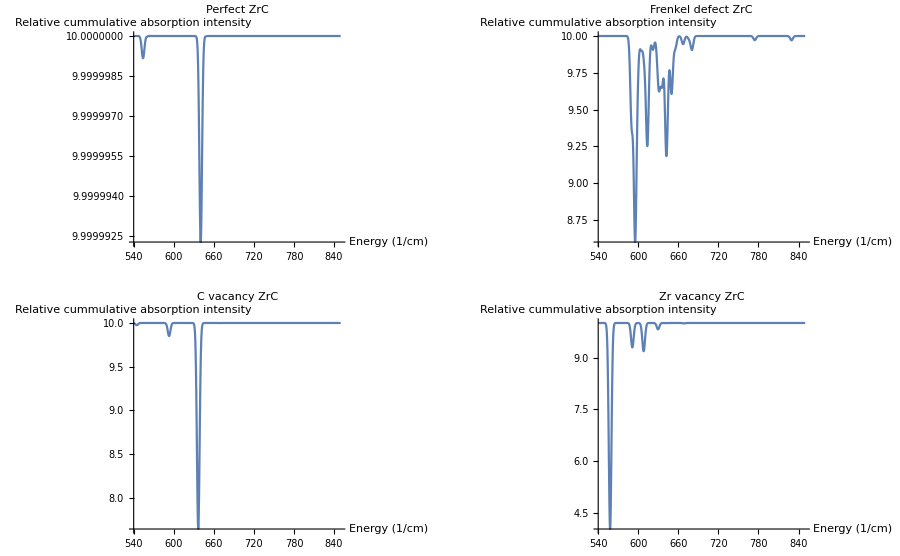

```mathematica
GraphicsGrid[{{p1,p2},{p3,p4}},ImageSize->900]
```

```mathematica
plotFun3[file_,name_]:=Plot[Total[Table[gauss[file[[i]]],{i,1,Length[file]}]],{x,540,850},PlotLabel->name,Evaluate@plotops2];
p1=plotFun3[dataPerf700,"Perfect ZrC"];
p2=plotFun3[dataFren700,"Frenkel defect ZrC"];
p3=plotFun3[dataCvac700,"C vacancy ZrC"];
p4=plotFun3[dataZvac700,"Zr vacancy ZrC"];
```

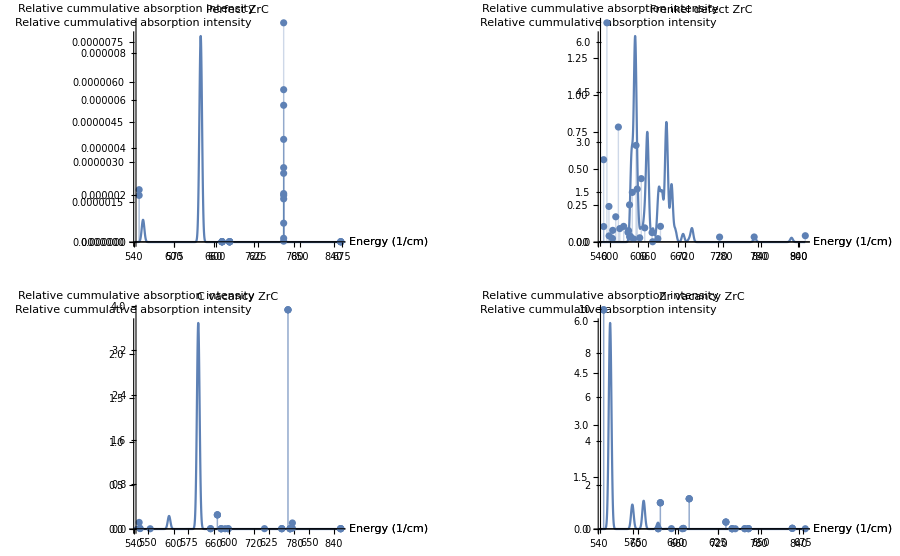

```mathematica
Show[GraphicsGrid[{{p1,p2},{p3,p4}},ImageSize->900],GraphicsGrid[{{ListPlot[dataPerf700,Filling->Axis,Evaluate@plotops2],ListPlot[dataFren700,Filling->Axis,Evaluate@plotops2]},{ListPlot[dataCvac700,Filling->Axis,Evaluate@plotops2],ListPlot[dataZvac700,Filling->Axis,Evaluate@plotops2]}},ImageSize->900]]
```